## Prerequisites

```mathematica
SetDirectory[Which[$FrontEnd=!=Null,NotebookDirectory[],$InputFileName=!="",DirectoryName[$InputFileName],True,"."]];
$ProjectRoot=RunProcess[{"git","rev-parse","--show-toplevel"}]["StandardOutput"]//StringTrim;

Needs["ResLept14041003`","1404.1003.m"];
Needs["NuFIT`","nufit40.m"];
Get["plot_tools.wl"];
msq=Get[FileNameJoin[{$ProjectRoot,"rge","msq.dat"}]];

RRep["NH",z_,ζ_]:={{0,Cos[z],ζ Sin[z]},{0,-Sin[z],ζ Cos[z]}};
RRep["IH",z_,ζ_]:={{Cos[z],ζ Sin[z],0},{-Sin[z],ζ Cos[z],0}};

Dagger=ConjugateTranspose;
MyPrecision=40;
MakePrecise[exp_]:=Module[{tmp,c},tmp=exp//.Complex[a_,b_]:>c[a,b]/.a_Real:>SetPrecision[a,MyPrecision];
tmp=tmp//.{c[a_,0.]:>a,Plus[a__,0.,b__]:>Plus[a,b]};
tmp/.c->Complex]

RemC[exp_]:=exp//.Complex[a_Real,0.]:>a;
CHOP[exp_]:=exp//Chop[#,1*^-30]&//N[#,10]&;
```

## Definitions

```mathematica
$Assumptions={vev>0,"(1/8π)">0};
hierarchy="IH";

$Assumptions=Join[$Assumptions,{Table[{Subscript[m, i]≥0,Subscript[rm, i]≥0,(Subscript[rm, i])^2==Subscript[m, i]},{i,3}],Table[{Subscript[M, a]>0,Subscript[rM, a]>0,(Subscript[rM, a])^2==Subscript[M, a]},{a,2}]}]//Flatten;
mm=DiagonalMatrix[{Subscript[m, 1],Subscript[m, 2],Subscript[m, 3]}];
MM=DiagonalMatrix[{Subscript[M, 1],Subscript[M, 2]}];
rmm=DiagonalMatrix[{Subscript[rm, 1],Subscript[rm, 2],Subscript[rm, 3]}];
rMM=DiagonalMatrix[{Subscript[rM, 1],Subscript[rM, 2]}];

$Assumptions=Join[$Assumptions,{w>0,y∈Reals,ζ∈Reals,ζ^2==1,δ>0,σ>0}]//Flatten;
$Assumptions=Join[$Assumptions,Table[{-1≤Subscript[co, x]≤1,-1≤Subscript[si, x]≤1,(Subscript[si, x])^2+(Subscript[co, x])^2==1},{x,{12,23,13}}]]//Flatten;
R = RRep[hierarchy,w+I y,ζ];
UPMNS={
{ Subscript[co, 12] Subscript[co, 13],  Subscript[si, 12] Subscript[co, 13], Subscript[si, 13] Conjugate[e]},
{-Subscript[si, 12] Subscript[co, 23] - Subscript[co, 12] Subscript[si, 23] Subscript[si, 13] e,  Subscript[co, 12] Subscript[co, 23] - Subscript[si, 12] Subscript[si, 23] Subscript[si, 13] e, Subscript[si, 23] Subscript[co, 13]},
{ Subscript[si, 12] Subscript[si, 23] - Subscript[co, 12] Subscript[co, 23] Subscript[si, 13] e, -Subscript[co, 12] Subscript[si, 23] - Subscript[si, 12] Subscript[co, 23] Subscript[si, 13] e, Subscript[co, 23] Subscript[co, 13]}
}.DiagonalMatrix[{1,Exp[I σ],1}]//.e->Exp[I δ];

$Assumptions=Join[$Assumptions,{Sinh2y∈Reals,Cosh2y≥1,Expy>0,Exp2y>0,Cosh2y^2==1+Sinh2y^2,Expy==√Exp2y,Cosh2y+Sinh2y==Exp2y}];
$Assumptions=Join[$Assumptions,{-1≤Sin2w≤1,-1≤Cos2w≤1,Sin2w^2+Cos2w^2==1}];
yrules = {Cosh[y]->(1+Sinh2y+Cosh2y)/(2 Expy),Sinh[y]->(-1+Sinh2y+Cosh2y)/(2 Expy)};
wrules = {Sin[2w]->Sin2w,Sin[w]^2->(1-Cos2w)/2,Cos[w]^2->(1+Cos2w)/2,Cos[2w]->Cos2w};
yrevert = {Expy->Exp[y],Exp2y->Exp[2y],Sinh2y->Sinh[2y],Cosh2y->Cosh[2y]};
ysimp = {Expy->√Exp2y,Exp2y->Sinh2y+Cosh2y,Cosh2y^2->1+Sinh2y^2};
wrevert = {Sin2w->Sin[2w], Cos2w->Cos[2w]};

$Assumptions=Join[$Assumptions, {mtot>0, ρm>0, δm>0, δM2>0}];
Mrules1 = {Subscript[M, 2]->Subscript[M, 1](1+δM),(Subscript[rm, a_])^2:>Subscript[m, a],(Subscript[rM, a_])^2:>Subscript[M, a]};
Mrules2 = {Subscript[M, 2]->Subscript[M, 1] √(1+δM2),(Subscript[rm, a_])^2:>Subscript[m, a],(Subscript[rM, a_])^2:>Subscript[M, a]};
mrules = Which[
  hierarchy==="NH", {Subscript[m, 2]->mtot/2 (1-ρm),Subscript[m, 3]->mtot/2 (1+ρm)},
  hierarchy==="IH", {Subscript[m, 1]->mtot/2 (1-ρm),Subscript[m, 2]->mtot/2 (1+ρm)},
  True, {}];
mrevert = Which[
  hierarchy==="NH", {ρm->(Subscript[m, 3]-Subscript[m, 2])/(Subscript[m, 2]+Subscript[m, 3]),mtot->Subscript[m, 2]+Subscript[m, 3]},
  hierarchy==="IH", {ρm->(Subscript[m, 2]-Subscript[m, 1])/(Subscript[m, 2]+Subscript[m, 1]),mtot->Subscript[m, 2]+Subscript[m, 1]},
  True, {}];
```

```mathematica
Y = ComplexExpand[(Sqrt[2]I/vev) rMM.R.rmm.Dagger[UPMNS]]//.yrules//Simplify;
Yc = ComplexExpand[Conjugate[(Sqrt[2]I/vev) rMM.R.rmm.Dagger[UPMNS]]]//.yrules//Simplify;
YYdag =2/vev^2 (ComplexExpand[rMM.R.mm.Dagger[R].rMM]//.yrules//Simplify)//.wrules//Simplify;
```

### Validation

```mathematica
yrules//.Rule->Equal//.yrevert//FullSimplify
wrules//.Rule->Equal//.wrevert//FullSimplify
Solve[Mrules1[[1]]//.Rule->Equal,{δM}]
Solve[Mrules2[[1]]//.Rule->Equal,{δM2}]
mrules//.Rule->Equal//.mrevert//FullSimplify
Simplify[Y.Transpose[Yc]-YYdag]//.wrevert
```

{True,True}

{True,True,True,True}

{{δM→(-M_1+M_2)/M_1}}

{{δM2→(-M_1^2+M_2^2)/M_1^2}}

{True,True}

{{0,0},{0,0}}

## Neutrino-option condition

```mathematica
Tneutopt = vev^2/2 Tr[YYdag]//.Join[mrules,Mrules1,yrevert]//FullSimplify
```

1/2 mtot (Cos2w δM ρm+(2+δM) Cosh[2 y]) M_1

```mathematica
Tneutopt/.{Cos2w->-1,y->0}//.mrevert//FullSimplify
Tneutopt/.δM->0
```

((1+δM) m_1+m_2) M_1

mtot Cosh[2 y] M_1

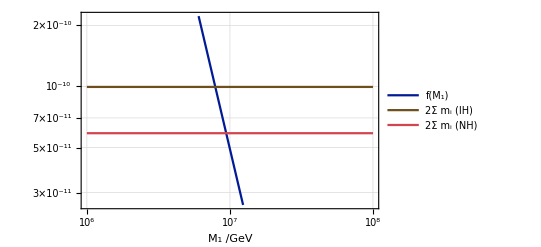

bfp2_fplot.pdf

```mathematica
fff=Function[M1,Module[{Q0=Exp[-3/4]M1,μsq,vev=246},
μsq=msq[Q0]/2; (* convention correction *)
μsq (M1^3/(16 π^2(vev^2/2)))^-1]];
LogLogPlot[{
fff[M1],
NuFIT`ToMasses[NuFIT`BestFit["IH"]]//Total,
NuFIT`ToMasses[NuFIT`BestFit["NH"]]//Total
},{M1,1*^6,1*^8},
PlotLegends->{"f(M_1)","2Σ m_i (IH)","2Σ m_i (NH)"},FrameLabel->{"M_1 /GeV"}]
outputPDF["fplot",%]
```

```mathematica
FindRoot[fff[M1]==(NuFIT`ToMasses[NuFIT`BestFit["NH"]]//Total), {M1, 1.01*^6}]
FindRoot[fff[M1]==(NuFIT`ToMasses[NuFIT`BestFit["IH"]]//Total), {M1, 1.01*^6}]
```

{M1→9.41717×10^6}

{M1→7.90186×10^6}

## Leptogenesis

```mathematica
F[i:1|2,a_]:=Module[{j=3-i},Im[Y[[i,a]]Yc[[j,a]]YYdag[[i,j]]]/(YYdag[[i,i]]YYdag[[j,j]])]
F2[i:1|2,a_]:=Module[{j=3-i},Im[Y[[i,a]]Yc[[j,a]]YYdag[[j,i]]]/(YYdag[[i,i]]YYdag[[j,j]])]
γ[i:1|2]:=YYdag[[i,i]]"(1/8π)"
Γ[i:1|2]:=Subscript[M, i] γ[i]
ρosc=Det[Re[YYdag]]/(YYdag[[1,1]]YYdag[[2,2]]);
fv[i:1|2]:=Module[{j=3-i},Γ[j]/Subscript[M, i](1-(1+Subscript[M, j]^2/Subscript[M, i]^2)Log[1+Subscript[M, i]^2/Subscript[M, j]^2])]
fm[i:1|2]:=Module[{j=3-i},((Subscript[M, i]^2-Subscript[M, j]^2)Subscript[M, i] Γ[j])/((Subscript[M, i]^2-Subscript[M, j]^2)^2+Subscript[M, i]^2Γ[j]^2)]
fo[i:1|2]:=Module[{j=3-i},((Subscript[M, i]^2-Subscript[M, j]^2)Subscript[M, i] Γ[j])/((Subscript[M, i]^2-Subscript[M, j]^2)^2+(Subscript[M, i] Γ[i]+Subscript[M, j] Γ[j])^2HoldForm[ρosc])]
```

Part::partd: Part specification YYdag⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification YYdag⟦2,2⟧ is longer than depth of object.

```mathematica
Series[fv[2]//.Mrules1//.mrules//.{"(1/8π)"->1/(8π)}//.yrevert,{δM,0,0}]//Normal//FullSimplify
Series[fv[1]//.Mrules1//.mrules//.{"(1/8π)"->1/(8π)}//.yrevert,{δM,0,0}]//Normal//FullSimplify
```

Part::partd: Part specification YYdag⟦1,1⟧ is longer than depth of object.

-((-1+Log[4]) YYdag⟦1,1⟧)/(8 π)

Part::partd: Part specification YYdag⟦2,2⟧ is longer than depth of object.

-((-1+Log[4]) YYdag⟦2,2⟧)/(8 π)

```mathematica
Series[fm[2]//.Mrules1//.mrules//.{"(1/8π)"->1/(8π)}//.yrevert,{δM,0,1}]//Normal//FullSimplify
Series[fm[1]//.Mrules1//.mrules//.{"(1/8π)"->1/(8π)}//.yrevert,{δM,0,1}]//Normal//FullSimplify
Series[Cosh[2 y]^2fo[2]//.Mrules1//.mrules//.{"(1/8π)"->1/(8π)}//.yrevert,{δM,0,1}]//Normal//FullSimplify
Series[Cosh[2 y]^2fo[1]//.Mrules1//.mrules//.{"(1/8π)"->1/(8π)}//.yrevert,{δM,0,1}]//Normal//FullSimplify
```

-(16 π vev^2 δM)/(Cos2w mtot ρm M_1-mtot Cosh[2 y] M_1)

-(16 π vev^2 δM)/(Cos2w mtot ρm M_1+mtot Cosh[2 y] M_1)

(4 π vev^2 δM (-Cos2w ρm+Cosh[2 y]))/(mtot ρosc M_1)

-(4 π vev^2 δM (Cos2w ρm+Cosh[2 y]))/(mtot ρosc M_1)

```mathematica
Fp[a_]:=F[1,a]+F2[1,a]+F[2,a]+F2[2,a]
Fm[a_]:=-F[1,a]-F2[1,a]+F[2,a]+F2[2,a]
```

```mathematica
{Fp[1],Fp[2],Fp[3]}//ComplexExpand//Simplify
```

{0,0,0}

```mathematica
{Fm1,Fm2,Fm3}={Fm[1],Fm[2],Fm[3]}//ComplexExpand//Simplify
```

{(2 Exp2y Sin2w co_13^2 (m_1-m_2) (2 si_12 (2 (1+Exp2y Sinh2y) ζ Sin[σ] co_12 rm_1 rm_2+Exp2y Sinh2y m_2 si_12)-2 Exp2y Sinh2y m_1 (-1+si_12^2)))/((1+2 Exp2y Sinh2y) ((Sin2w^2+Sinh2y^2) m_1^2+2 (2-Sin2w^2+Sinh2y^2) m_1 m_2+(Sin2w^2+Sinh2y^2) m_2^2)),(4 Exp2y Sin2w (m_1-m_2) (Exp2y Sinh2y m_1 si_12^2+2 ζ Sin[δ-σ] co_23 rm_1 rm_2 si_13 si_23+2 Exp2y Sinh2y ζ Sin[δ-σ] co_23 rm_1 rm_2 si_13 si_23+4 ζ Cos[δ] Sin[σ] co_23 rm_1 rm_2 si_12^2 si_13 si_23+4 Exp2y Sinh2y ζ Cos[δ] Sin[σ] co_23 rm_1 rm_2 si_12^2 si_13 si_23-Exp2y Sinh2y m_1 si_12^2 si_23^2+Exp2y Sinh2y m_1 si_13^2 si_23^2-Exp2y Sinh2y m_1 si_12^2 si_13^2 si_23^2+2 co_12 si_12 (Exp2y Sinh2y Cos[δ] co_23 m_1 si_13 si_23+(1+Exp2y Sinh2y) ζ Sin[σ] rm_1 rm_2 (-1+(1+si_13^2) si_23^2))+Exp2y Sinh2y m_2 (1-2 Cos[δ] co_12 co_23 si_12 si_13 si_23-si_23^2+si_12^2 (-1+(1+si_13^2) si_23^2))))/((1+2 Exp2y Sinh2y) ((Sin2w^2+Sinh2y^2) m_1^2+2 (2-Sin2w^2+Sinh2y^2) m_1 m_2+(Sin2w^2+Sinh2y^2) m_2^2)),(4 Exp2y Sin2w (m_1-m_2) (Exp2y Sinh2y m_2 si_12^2 si_13^2-2 ζ Sin[δ-σ] co_23 rm_1 rm_2 si_13 si_23-2 Exp2y Sinh2y ζ Sin[δ-σ] co_23 rm_1 rm_2 si_13 si_23-4 ζ Cos[δ] Sin[σ] co_23 rm_1 rm_2 si_12^2 si_13 si_23-4 Exp2y Sinh2y ζ Cos[δ] Sin[σ] co_23 rm_1 rm_2 si_12^2 si_13 si_23+Exp2y Sinh2y m_2 si_23^2-Exp2y Sinh2y m_2 si_12^2 si_23^2-Exp2y Sinh2y m_2 si_12^2 si_13^2 si_23^2+Exp2y Sinh2y m_1 (-2 Cos[δ] co_12 co_23 si_12 si_13 si_23+si_12^2 si_23^2+(-1+si_12^2) si_13^2 (-1+si_23^2))-2 co_12 si_12 (-Exp2y Sinh2y Cos[δ] co_23 m_2 si_13 si_23+(1+Exp2y Sinh2y) ζ Sin[σ] rm_1 rm_2 (si_23^2+si_13^2 (-1+si_23^2)))))/((1+2 Exp2y Sinh2y) ((Sin2w^2+Sinh2y^2) m_1^2+2 (2-Sin2w^2+Sinh2y^2) m_1 m_2+(Sin2w^2+Sinh2y^2) m_2^2))}

```mathematica
((2ρm Sin[2w])/(1-ρm^2+ρm^2 Sin[2 w]^2+Sinh[2 y]^2))^-1 Fm1//.yrevert//.wrevert//.mrules//FullSimplify
(4 Subscript[rm, 1] Subscript[rm, 2])/mtot ζ Cosh[2y]Im[UPMNS[[1,1]]Conjugate[UPMNS[[1,2]]]]-Sinh[2y](
(1+ρm)UPMNS[[1,2]]Conjugate[UPMNS[[1,2]]]+(1-ρm)UPMNS[[1,1]]Conjugate[UPMNS[[1,1]]])-%//Simplify//ComplexExpand
```

((4 ζ Cosh[2 y] Sin[σ] co_12 rm_1 rm_2 si_12+mtot Sinh[2 y] (1-ρm+2 ρm si_12^2)) (-1+si_13^2))/mtot

0

```mathematica
((2ρm Sin[2w])/(1-ρm^2+ρm^2 Sin[2 w]^2+Sinh[2 y]^2))^-1 Fm2//.yrevert//.wrevert//.mrules//Collect[#,{Subscript[co, _],Subscript[si, _]},FullSimplify]&
(4 Subscript[rm, 1] Subscript[rm, 2])/mtot ζ Cosh[2y]Im[UPMNS[[2,1]]Conjugate[UPMNS[[2,2]]]]-Sinh[2y](
(1+ρm)UPMNS[[2,2]]Conjugate[UPMNS[[2,2]]]+(1-ρm)UPMNS[[2,1]]Conjugate[UPMNS[[2,1]]])-%//Simplify//ComplexExpand//FullSimplify
```

-(1+ρm) Sinh[2 y]+(1+ρm) Sinh[2 y] si_23^2+(-1+ρm) Sinh[2 y] si_13^2 si_23^2+co_23 (-(4 ζ Cosh[2 y] Sin[δ-σ] rm_1 rm_2 si_13 si_23)/mtot-(8 ζ Cos[δ] Cosh[2 y] Sin[σ] rm_1 rm_2 si_12^2 si_13 si_23)/mtot)+si_12^2 (2 ρm Sinh[2 y]-2 ρm Sinh[2 y] si_23^2-2 ρm Sinh[2 y] si_13^2 si_23^2)+co_12 (4 ρm Cos[δ] Sinh[2 y] co_23 si_12 si_13 si_23+si_12 ((4 ζ Cosh[2 y] Sin[σ] rm_1 rm_2)/mtot-(4 ζ Cosh[2 y] Sin[σ] rm_1 rm_2 si_23^2)/mtot-(4 ζ Cosh[2 y] Sin[σ] rm_1 rm_2 si_13^2 si_23^2)/mtot))

0

```mathematica
((2ρm Sin[2w])/(1-ρm^2+ρm^2 Sin[2 w]^2+Sinh[2 y]^2))^-1 Fm3//.yrevert//.wrevert//.mrules//Collect[#,{Subscript[co, _],Subscript[si, _]},FullSimplify]&
(4 Subscript[rm, 1] Subscript[rm, 2])/mtot ζ Cosh[2y]Im[UPMNS[[3,1]]Conjugate[UPMNS[[3,2]]]]-Sinh[2y](
(1+ρm)UPMNS[[3,2]]Conjugate[UPMNS[[3,2]]]+(1-ρm)UPMNS[[3,1]]Conjugate[UPMNS[[3,1]]])-%//Simplify//ComplexExpand//FullSimplify
```

-(1+ρm) Sinh[2 y] si_23^2+2 ρm Sinh[2 y] si_12^2 si_23^2+co_23 si_13 ((4 ζ Cosh[2 y] Sin[δ-σ] rm_1 rm_2 si_23)/mtot+(8 ζ Cos[δ] Cosh[2 y] Sin[σ] rm_1 rm_2 si_12^2 si_23)/mtot)+si_13^2 ((-1+ρm) Sinh[2 y]-(-1+ρm) Sinh[2 y] si_23^2+si_12^2 (-2 ρm Sinh[2 y]+2 ρm Sinh[2 y] si_23^2))+co_12 (-4 ρm Cos[δ] Sinh[2 y] co_23 si_12 si_13 si_23+(4 ζ Cosh[2 y] Sin[σ] rm_1 rm_2 si_12 si_23^2)/mtot+si_12 si_13^2 (-(4 ζ Cosh[2 y] Sin[σ] rm_1 rm_2)/mtot+(4 ζ Cosh[2 y] Sin[σ] rm_1 rm_2 si_23^2)/mtot))

0

```mathematica
((2ρm Sin[2w])/(1-ρm^2+ρm^2 Sin[2 w]^2+Sinh[2 y]^2))^-1 Fm2//.yrevert//.wrevert//.mrules//Simplify;
%//Collect[#,{Subscript[co, _],Subscript[si, _]},FullSimplify]&;
Collect[%,{Cosh[2y],Sinh[2y]},FullSimplify]
%+Sinh[2y]((1+ρm) Subscript[co, 13]^2 Subscript[si, 23]^2+(1-ρm) (Subscript[co, 12]^2 Subscript[co, 23]^2-2 Cos[δ] Subscript[co, 12] Subscript[co, 23] Subscript[si, 12] Subscript[si, 13] Subscript[si, 23]+Subscript[si, 12]^2 Subscript[si, 13]^2 Subscript[si, 23]^2)
)//FullSimplify
```

```mathematica
((2ρm Sin[2w])/(1-ρm^2+ρm^2 Sin[2 w]^2+Sinh[2 y]^2))^-1 Fm3//.yrevert//.wrevert//.mrules//Simplify;
%//Collect[#,{Subscript[co, _],Subscript[si, _]},FullSimplify]&;
Collect[%,{Cosh[2y],Sinh[2y]},FullSimplify]
-Subscript[co, 23] Subscript[co, 13] (Sin[σ] Subscript[co, 12] Subscript[si, 23]+Sin[δ+σ] Subscript[si, 12] Subscript[si, 13] Subscript[co, 23])4ζ Cosh[2y](Subscript[rm, 2] Subscript[rm, 3])/mtot-(1-Subscript[co, 12]^2 Subscript[co, 23]^2 Subscript[si, 13]^2-Subscript[si, 12]^2 Subscript[si, 23]^2+ρm (Subscript[co, 13]^2 Subscript[co, 23]^2-Subscript[co, 23]^2 Subscript[si, 12]^2 Subscript[si, 13]^2-Subscript[co, 12]^2 Subscript[si, 23]^2)+2 (1-ρm) Cos[δ] Subscript[co, 12] Subscript[co, 23] Subscript[si, 12] Subscript[si, 13] Subscript[si, 23]
 )Sinh[2y]-%//FullSimplify
```